```mathematica
Simplify[Solve[
{a0+ lambda b0 + nu c0 == x0,a1 + lambda b1 + nu c1 == x1},{lambda,nu}]]
```

{{lambda→(a1 c0-a0 c1+c1 x0-c0 x1)/(-b1 c0+b0 c1),nu→(a1 b0-a0 b1+b1 x0-b0 x1)/(b1 c0-b0 c1)}}

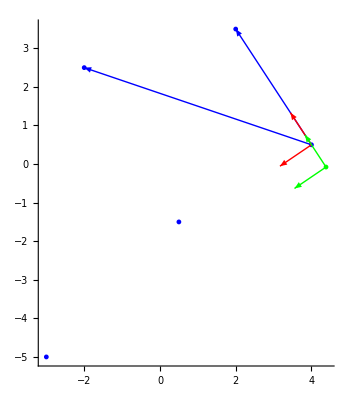

```mathematica
(* Radius for the disks - we visualize points with those *)
dr=  0.0625;
(* Arbitrary point set (has to have at least 3 points) *)
points={{4,0.5},{2,3.5},{-2,2.5},{0.5,-1.5},{-3,-5}};
(* We build a two-dimensional parameter equation from the first three vertices (the two blue arrows in the picture) *)
a=points[[1]];
b=points[[2]]-a;
c=points[[3]]-a;
(* Orthonormalize the vectors. I think we have to do this because then the two parameters in the parameter equation are separated, see below for why this is important *)
ortho=Orthogonalize[{b,c}];orthob=ortho[[1]];orthoc=ortho[[2]];
(* 
This looks intimidating, but is quite simple: All our points are on the plane, 
so every point "x" can be expressed with the plane vectors:
x = a + lambda * b + nu * c
We're interested in the coefficients lambda and nu, so we Solve[] the equation system for those variables. That's where those strange calculations below stem from.
 *)
texcoords=
Map[
{
(a[[2]]*orthoc[[1]]-a[[1]]*orthoc[[2]]+orthoc[[2]]*#1[[1]]-orthoc[[1]]*#1[[2]])/(orthob[[1]]*orthoc[[2]]-orthob[[2]]*orthoc[[1]]),(a[[2]]*orthob[[1]]-a[[1]]*orthob[[2]]+orthob[[2]]*#1[[1]]-orthob[[1]]*#1[[2]])/(orthob[[2]]*orthoc[[1]]-orthob[[1]]*orthoc[[2]])
}&,
points];
(* We want the lowest coefficients. Those specify the origin of the texture coordinate system (seen below in green) *)
texmins={Fold[Min[#1,#2[[1]]]&,texcoords[[1]][[1]],texcoords],Fold[Min[#1,#2[[2]]]&,texcoords[[1]][[2]],texcoords]};
neworigin = a + texmins[[1]]*orthob+texmins[[2]]*orthoc;
Graphics[
Join[
{
Blue
},
Map[
Disk[#1,dr]&,
points],
{
Arrow[{a,a+b}],
Arrow[{a,a +c}],
Red,
Arrow[{a,a+orthob}],
Arrow[{a,a +orthoc}],
Green,
Disk[neworigin,dr],
Arrow[{neworigin,neworigin+orthob}],
Arrow[{neworigin,neworigin +orthoc}]
}],
Axes->True]
```